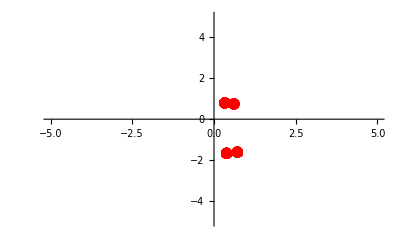

```mathematica
(*CHAOS!*)
Remove["Global`*"]

(*Damped driven pendulum generic*)
diffeq = {θ''[t]+c θ'[t]+Sin[θ[t]]==F Cos[Ω t]};
iclist = {θ[0]==θ0,θ'[0]==ω0};
eqnlist = Join[diffeq,iclist];
(*Numerical soln needs numbers*)

(*Parameters*)
c=0.05;
Ω=0.901;
F= 0.7;(*0.6*)

(*Initial conditions*)
θ0=1.0;
ω0 = 0;


(*Useful stuff*)
T=2π/Ω;
tmin = 80 T;
tmax= 200T;
tstep=T;

(*Mapping function*)
map[x_]:=Mod[x,2π]/;Mod[x,2π]<=π;
map[x_]:=(Mod[x,2π]-2π)/;Mod[x,2π]>π;
(*Solve it*)
soln = NDSolve[eqnlist,θ,{t,tmin,tmax},MaxSteps->∞][[1]];

(*Plots plots plots*)

(*Poincare plot*)
plist = Table[{map[θ[t]],θ'[t]}/.soln,{t,tmin,tmax,tstep}];
Print[ListPlot[plist,PlotRange->5{{-1,1},{-1,1}},PlotStyle->{Red,PointSize[0.02]}]]

(*Phase plot*)
traj=ParametricPlot[{map[θ[t]],θ'[t]}/.soln,{t,tmin,tmax},PlotStyle->{Red},PlotRange->1.3{{-π,π},{-3,3}}];

L= 5.;
string[t_]:=Graphics[{Line[{{0,0},L{Sin[map[θ[t]]],-Cos[map[θ[t]]]}}/.soln]}]
bob[t_]:=Graphics[{PointSize[0.02],Point[L{Sin[map[θ[t]]],-Cos[map[θ[t]]]}/.soln]}]
pix1[t_]:=Show[string[t],bob[t],PlotRange->7{{-1,1},{-1,1}},Axes->True]
pt[t_]:=Graphics[{PointSize[0.02],Point[{map[θ[t]],θ'[t]}/.soln]}]
pix2[t_]:=Show[traj,pt[t]]
Print[Animate[
GraphicsGrid[{{pix1[t],pix2[t]}}],{t,tmin,tmax},ControlPlacement->Top,AnimationRate->.5]]
```

Searching for Chaos in Population Models

**********************************************************************************************

A Naive Growth Model

A simple growth model for a population which uses discrete time intervals is given by the equation:

x[n] = α x[n-1],   α > 0

Let's take our discrete time interval to be four monnths.
In that case this equation says that the population now is α times what it was 4 months ago.

This model is too simplistic to create chaotic behavior.
There is a simple equation relating x[n] to the growth constant (α) and initial population (x[0] ≡ x_0):
x[n] = α^n x_0

**********************************************************************************************

The Logistic Map

To better model population, let's take x to be the population as a proportion of the carrying capacity.
Then we add a (1-x) term, so that growth rate slows near this capacity:
x[n] = α x[n-1](1 - x[n-1])

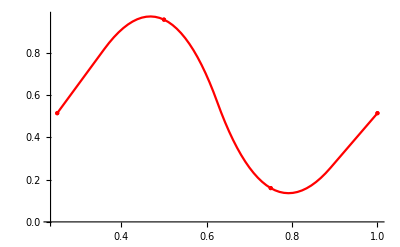

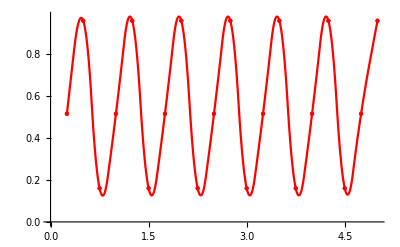

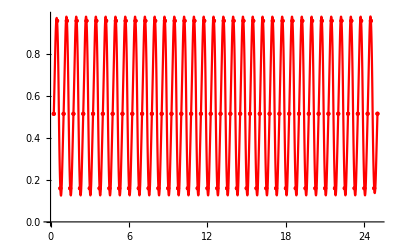

```mathematica
Remove["Global`*"]
Print[Style["Searching for Chaos in Population Models","Title"]]
Print["**********************************************************************************************"]
Print["\n",Style["A Naive Growth Model","Chapter",Bold]]
x[n_]:=x[n]=α x[n-1](1-x[n-1]);
Print["A simple growth model for a population which uses discrete time intervals is given by the equation:"]
Print["x[n] = α x[n-1],   α > 0"]
Print["Let's take our discrete time interval to be four monnths.\nIn that case this equation says that the population now is α times what it was 4 months ago."]
Print["This model is too simplistic to create chaotic behavior.\nThere is a simple equation relating x[n] to the growth constant (α) and initial population (x[0] ≡ x_0):\nx[n] = α^n x_0"]
Print["**********************************************************************************************"]
Print["\n",Style["The Logistic Map","Chapter",Bold]]
Print["To better model population, let's take x to be the population as a proportion of the carrying capacity.\nThen we add a (1-x) term, so that growth rate slows near this capacity:\nx[n] = α x[n-1](1 - x[n-1])"]
α=3.82842;
x[1] =0.514;
data[nmax_]:= Table[{n/4,x[n]},{n,1,nmax}]
plot[n_]:=ListPlot[data[n]]
Print[ListPlot[data[4],Mesh->Full,InterpolationOrder->2,Joined->True,PlotStyle->{Red,PointSize[Large]}]]
Print[ListPlot[data[20],Mesh->Full,InterpolationOrder->2,Joined->True,PlotStyle->{Red,PointSize[Medium]}]]
Print[ListPlot[data[100],Mesh->Full,InterpolationOrder->2,Joined->True,PlotStyle->{Red,PointSize[Small]}]]
```